## RK Code

RK Schemes are going to be specified by Extended Butcher Tables of the form
	c | A
  | b_H
b_L 
where A is a strictly lower triangular matrix of substep weights, c is the vector of inner substep lengths, b_H is the vector pf high precision final slope weights, and b_Lis the vector of low precision final slope weights.

We want to make a general RK individual step procedure and a general step control mechanism.  We are going to mimic the input and output of our development Bogacki-Shampine code.

```mathematica
BSTable=Association[{
"A"->({{0, 0, 0, 0}, {1/2, 0, 0, 0}, {0, 3/4, 0, 0}, {2/9, 1/3, 4/9, 0}}),
"bH"->{2/9,1/3,4/9,0},"orderH"->3,
"bL"->{7/24,1/4,1/3,1/8},"orderL"->2,
"c"->{0,1/2,3/4,1}
}];
```

```mathematica
RKStep[f_,BT_][{h_,t0_,y0_}]:= Module[
{A,bH,bL,c,p,s,z,K},
(* Extract Data from Association *)
{A,bH,bL,c,p}=Map[BT,{"A","bH","bL","c","orderL"}];
s=Length[A];
(* Assign space for and compute internal slopes *)
K=ConstantArray[0.0,{Length[y0],s}];
Do[
z=y0+h*Sum[A⟦i,j⟧ K⟦All,j⟧,{j,1,i-1}];
K⟦All,i⟧=f[t0+c⟦i⟧h,z],
{i,1,s}]; 
(* Compute and return potential updated t, yH, and yL *)
{t0+h, 
y0+h*Sum[bH⟦i⟧K⟦All,i⟧,{i,1,s}], (*High Order*)
y0+h*Sum[bL⟦i⟧K⟦All,i⟧,{i,1,s}]}
]
```

Lets test on the worlds simplest ODE system. 
	y'=y  
with y(0)={1.0} and solution y(t)={E^t}.

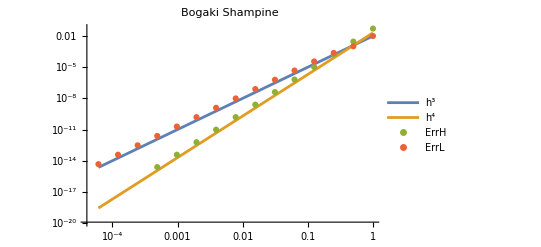

```mathematica
f[t_,y_]:=y
t0=0.1;y0={1.0};
hs=Table[0.5^p,{p,0,14}];
{ErrHs,ErrLs}=Table[
{t,yH,yL}=RKStep[f,BSTable][{h,t0,y0}];
{Norm[{E^h}-yH],Norm[{E^h}-yL]},
{h,hs}]ᵀ;
ListLogLogPlot[{
{hs,0.01 hs^3}ᵀ,{hs,0.02 hs^4}ᵀ,
{hs,ErrHs}ᵀ,{hs,ErrLs}ᵀ
},
Joined->{True,True, False,False},
PlotLegends->{"h^3","h^4","ErrH","ErrL"},
PlotRange->All,
PlotLabel->"Bogaki Shampine"]
```

The Dormand-Prince pair are the parameters used in ODE45. The values are taken from https://en.wikipedia.org/wiki/Dormand%E2%80%93Prince_method

```mathematica
DorPrinceTable=Association[{
"A"->({{0, 0, 0, 0, 0, 0}, {1/5, 0, 0, 0, 0, 0}, {3/40, 9/40, 0, 0, 0, 0}, {44/45, -56/15, 32/9, 0, 0, 0}, {19372/6561, -25360/2187, 64448/6561, -212/729, 0, 0}, {9017/3168, -355/33, 46732/5247, 49/176, -5103/18656, 0}, {35/384, 0, 500/1113, 125/192, -2187/6784, 11/84}}),
"bH"->{35/384, 0, 500/1113, 125/192,-2187/6784, 11/84,0},"orderH"->5,
"bL"->{5179/57600, 0, 7571/16695, 393/640,−92097/339200,187/2100, 1/40},
"orderL"->4,
"c"->{0, 1/5, 3/10, 4/5,8/9,1, 1}
}];
```

As always we should check that they have the claimed error.

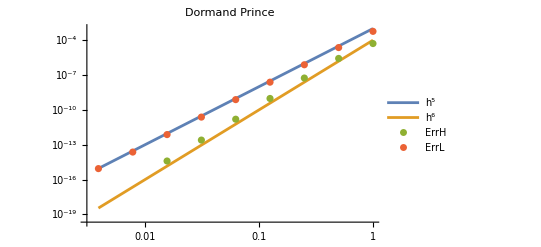

```mathematica
f[t_,y_]:=y
t0=0.1;y0={1.0};
hs=Table[0.5^p,{p,0,8}];
{ErrHs,ErrLs}=Table[
{t,yH,yL}=RKStep[f,DorPrinceTable][{h,t0,y0}];
{Norm[{E^h}-yH],Norm[{E^h}-yL]},
{h,hs}]ᵀ;
ListLogLogPlot[{
{hs,0.001 hs^5}ᵀ,{hs,0.0001 hs^6}ᵀ,
{hs,ErrHs}ᵀ,{hs,ErrLs}ᵀ
},
Joined->{True,True, False,False},
PlotLegends->{"h^5","h^6","ErrH","ErrL"},
PlotRange->All,
PlotLabel->"Dormand Prince"]
```

Things to notice:  I had to put small numbers into the comparison lines to shift them down.  I had to not take tiny steps so that the errors did not get below the 10^-16 floor from standard double-precision arithmetic.

The higher order schemes can be more efficient because they can take much larger  steps.

## Step Size Control

As a reminder, the standard step size control estimates the error using the two different order solutions yH and yL.  The scheme takes a step if the error estimate is less than the tolerance and skips the step if it is not.  In either case the scheme estimates the maximum step using the lower order with a safety factor of 0.9.

We need to think about how people use an ODE solver.

The development code is below.

## Fancy Ralston Method

### Step Length Prediction

In practice, we want to make sure that our errors at each step are less than some tolerance. A typical tolerance is Tol=10^-7.

After an FR step of size h the error ||y-w||=err≈C_2 h^3.  If err>Tol then h was too large and it makes sense to try again with a scaled step γ h.   The expected error with a scaled step γ h is 
	(C_2(γ h))^3=C_2 h^3 γ^3=err γ^3
If all the estimates were exact the tolerance would be hit if   
	Tol=(C_2(γ h))^3=C_2 h^3 γ^3=err γ^3.
The step size control follows from 
	γ=(Tol/err)^(1/3) 
In practice the more cautious scheme 
	γ=(0.9Tol/err)^(1/3) 
is implemented that tries to satisfy
	0.9 Tol=err γ^3.

When||y-w||=err>Tol the step is bad: skip the update and try again with the smaller step size γ h where γ=(0.9Tol/err)^(1/3)<1.

When||y-w||=err≤Tol the step is good: take the best update z and try the next step with the adjusted step size γ h where γ=(0.9Tol/err)^(1/3)>1.

### Bogaki-Shampine ODE23

The Bogaki-Shampine pair is simply the code in FR with step-size control based on the above.

```mathematica
BogakiShampineStep[f_,Tol_][{t_,y_,h_}]:= Module[{tNew,w,z,err,γ},
{tNew,w,z}=FancyRalstonStep[f,h][{t,y}];
err=Norm[w-z];
γ=(0.9Tol/err)^(1/3);
If[ err≥Tol,
{t,y,γ h},
{tNew,z,γ h}]
]
```

```mathematica
Clear[SynSol,ySol, f,t,y,g]
SynSol[t_]:= {Cos[t+Sin[t]], Sin[t] - Cos[Sin[t]-ArcTan[Cos[ t+ 2]+t]]}
g[t_,{y1_,y2_}]:={3.2 (y2+Sin[2 t]^2)Cos[t+y1], 2.3 t + Sin[t + y2]};
ff[t_]= Simplify[ SynSol'[t]-g[t,SynSol[t]]];
f[t_,y_]:=g[t,y]+ff[t]
t0=0.1; y0=SynSol[t0];
TMax=3.4;
ySol=NDSolveValue[ {y'[t]==f[t,y[t]],y[t0]==y0},y,{t,t0, t0+TMax}];
ODESteps=50;
{Tol,h0}={10^-5,0.1};
Data=NestList[BogakiShampineStep[f,Tol],{t0,y0,h0},ODESteps];
TabView[{
"Sol"->ParametricPlot[ySol[t],{t,t0, TMax},
Epilog->Point[Data⟦All,2⟧]],
"StepSize"->ListLogPlot[Data⟦All,3⟧,
PlotRange->All,
GridLines->Automatic,
Frame->True,
FrameLabel->{"i","h"}]
}
]
```

12

## Lotka Volterra Equations

We are going to test the code on the Lotka-Volterra equations from https://en.wikipedia.org/wiki/Lotka%E2%80%93Volterra_equations

```mathematica
LV[{α_,β_,γ_,δ_}][t_,{x_,y_}]:= {α x - β x y, -γ y + δ x y}
params={0.1,0.2,0.3,0.4}; TMax=50.4; t0=0.1;y0={0.1,0.2};
```